```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["results_ToricEven.xlsx"][[1]];
sNames=s[[1]]
sData=s[[2;;]]
sData[[;;,1]]
```

{p,L,I,varI}

{{0.01,4.,0.0203482,1.91×10^-8},{0.01,6.,0.00210683,2.6×10^-9},{0.01,8.,0.000172583,2.66×10^-10},{0.01,10.,0.0000237,4.4×10^-11},{0.02,4.,0.0614899,4.62×10^-8},{0.02,6.,0.0135489,1.42×10^-8},{0.02,8.,0.00338513,3.66×10^-9},{0.02,10.,0.000608776,8.12×10^-10},{0.03,4.,0.112207,7.08×10^-8},{0.03,6.,0.044175,3.45×10^-8},{0.03,8.,0.0179061,1.45187×10^-8},{0.03,10.,0.00549873,5.43×10^-9},{0.04,4.,0.1616,8.81×10^-8},{0.04,6.,0.112295,5.8×10^-8},{0.04,8.,0.0573678,3.44×10^-8},{0.04,10.,0.0248488,},{0.05,4.,0.204878,9.7×10^-8},{0.05,6.,0.101714,1.84×10^-6},{0.05,8.,0.132664,5.96×10^-8},{0.05,10.,0.0738913,},{0.06,4.,0.238538,9.76×10^-8},{0.06,6.,0.186364,1.31×10^-7},{0.06,8.,0.246046,8.13×10^-8},{0.06,10.,0.16728,}}

{0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.06,0.06,0.06,0.06}

{{{4.,0.020350.00028},{6.,0.002110.00010},{8.,0.0001730.000033},{10.,0.0000240.000013}},{{4.,0.06150.0004},{6.,0.013550.00024},{8.,0.003390.00012},{10.,0.000610.00006}},{{4.,0.11220.0005},{6.,0.04420.0004},{8.,0.017910.00024},{10.,0.005500.00015}},{{4.,0.16160.0006},{6.,0.11230.0005},{8.,0.05740.0004},{10.,0.02484882 √}},{{4.,0.20490.0006},{6.,0.10170.0027},{8.,0.13270.0005},{10.,0.07389132 √}},{{4.,0.23850.0006},{6.,0.18640.0007},{8.,0.24600.0006},{10.,0.167282 √}}}

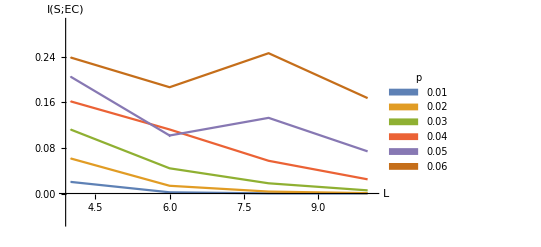

results_Even.pdf

```mathematica
Transpose[{sData[[;;,3]],2*Sqrt[sData[[;;,3]]]}];
Data=Apply[Around,Transpose[{sData[[;;,3]],2*Sqrt[sData[[;;,4]]]}],1];
DataPlot=Partition[Transpose[{sData[[;;,2]],Data}],4]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{3.9,10.1},{-0.05,0.3}},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["results_Even.pdf",plot]
```